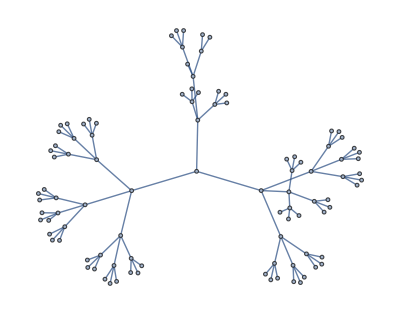

```mathematica
KaryTree[99,3]
```

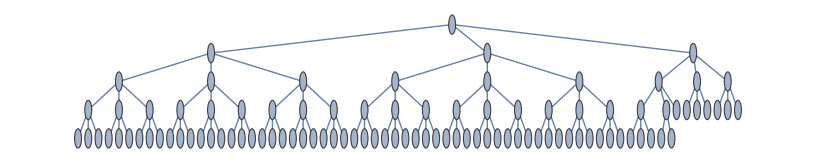

```mathematica
(VertexDegree[KaryTree[99,3]]//Counts)[1]
```

66

```mathematica
Log[3,99]//N
```

4.18266

```mathematica
3^2
```

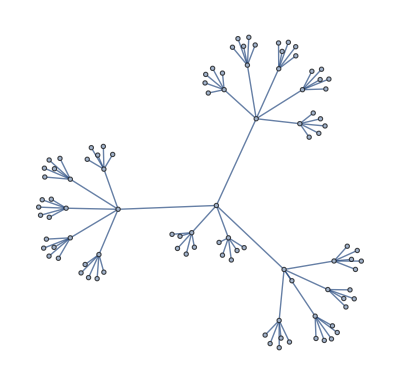

```mathematica
KaryTree[100,5]
```

```mathematica
VertexCount[%12]
```

100

```mathematica
Solve[99==(3l-1)/(3-1),l]//N
```

{{l→66.3333}}

```mathematica
(VertexDegree[KaryTree[100,5]]//Counts)[1]
```

80

```mathematica
freq=<|"A"->0.10, "B"-> 0.25, "C"-> 0.05, "D"->0.15, "E"-> 0.30, "F"-> 0.07, "G"-> 0.08|>
```

<|A→0.1,B→0.25,C→0.05,D→0.15,E→0.3,F→0.07,G→0.08|>

```mathematica
(#1 100&)/@freq
```

<|A→10.,B→25.,C→5.,D→15.,E→30.,F→7.,G→8.|>

```mathematica
#/.(x_->y_)->{x,y}
```

{a,1}

```mathematica
counts=(#1 100&)/@freq
```

<|A→10.,B→25.,C→5.,D→15.,E→30.,F→7.,G→8.|>

```mathematica
MapThread[Table[#1,#2]&,{Keys[counts],Values[counts]}]//Flatten
```

```mathematica
str={"A","A","A","A","A","A","A","A","A","A","B","B","B","B","B","B","B","B","B","B","B","B","B","B","B","B","B","B","B","B","B","B","B","B","B","C","C","C","C","C","D","D","D","D","D","D","D","D","D","D","D","D","D","D","D","E","E","E","E","E","E","E","E","E","E","E","E","E","E","E","E","E","E","E","E","E","E","E","E","E","E","E","E","E","E","F","F","F","F","F","F","F","G","G","G","G","G","G","G","G"}
```

{A,A,A,A,A,A,A,A,A,A,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,C,C,C,C,C,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,E,E,E,E,E,E,E,E,E,E,E,E,E,E,E,E,E,E,E,E,E,E,E,E,E,E,E,E,E,E,F,F,F,F,F,F,F,G,G,G,G,G,G,G,G}

```mathematica
bits=
<|"A"->"110",
"B"->"10",
"C"->"0111",
"D"->"010",
"E"->"00",
"F"->"0110",
"G"->"111"|>//Map[Characters@*Map[IntegerDigits]]
```

<|A→{1,1,0},B→{1,0},C→{0,1,1,1},D→{0,1,0},E→{0,0},F→{0,1,1,0},G→{1,1,1}|>

```mathematica
bs=str/.Normal[bits]//Flatten
```

{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Length[bs]
```

257

```mathematica
DepthFirstScan[-Graphics-,1,{"PrevisitVertex"->(Print["Visiting ",#]&)}]
```

Visiting 1

Visiting 2

Visiting 4

Visiting 5

Visiting 3

Visiting 6

Visiting 7

{1,1,1,2,2,3,3}

```mathematica
Clear[g]
```

```mathematica
Clear[n]
```

```mathematica
(Map[#/.(x_<->y_)->ToString[x]<->ToString[y]&])/@{
a<->b,a<->g,
g<->l,g<->h,
b<->c,
c<->h,
h<->m,h<->i,
i<->d,i<->j,i<->e,
d<->e,
e<->j,e<->f,
f<->k,
j<->n,j<->k}
```

{a<->b,a<->g,g<->l,g<->h,b<->c,c<->h,h<->m,h<->i,i<->d,i<->j,i<->e,d<->e,e<->j,e<->f,f<->k,j<->n,j<->k}

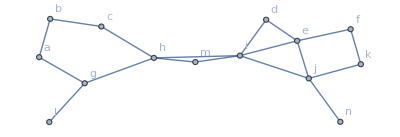

```mathematica
graph=Graph[(*(Map[#/.(x_<->y_)->ToString[x]<->ToString[y]&])/@*){
a<->b,a<->g,
g<->l,g<->h,
b<->c,
c<->h,
h<->m,h<->i,
m<->i,
i<->d,i<->j,i<->e,
d<->e,
e<->j,e<->f,
f<->k,
j<->n,j<->k},VertexLabels->"Name"]
```

```mathematica
graph//DepthFirstScan[#,a,{"PrevisitVertex"->(Print["Visiting ",#]&)}]&
```

Visiting a

Visiting b

Visiting c

Visiting h

Visiting g

Visiting l

Visiting m

Visiting i

Visiting d

Visiting e

Visiting j

Visiting n

Visiting k

Visiting f

{a,a,h,g,c,b,h,m,i,e,d,k,j,j}